```mathematica
ClearAll[m0];ClearAll[Γ0];ClearAll[S];ClearAll[L0];
ClearAll[decs];ClearAll[BR];

m0[p[938]]=0.938;Γ0[p[938]]=0.;S[p[938]]=1/2;L0[p[938]]=0;

m0[p[1440]]=1.440;Γ0[p[1440]]=0.200;S[p[1440]]=1/2;L0[p[1440]]=0;
decays[p[1440]]={{p[938],pi},{p[938],pipi},{Δ[1232],pi}};
BR[p[1440],{p[938],pi}]=0.70;
BR[p[1440],{p[938],pipi}]=0.05;
BR[p[1440],{Δ[1232],pi}]=0.25;

m0[p[1520]]=1.520;Γ0[p[1520]]=0.125;S[p[2]]=3/2;L0[p[1520]]=1;
decays[p[1520]]={{p[938],pi},{p[938],pipi},{Δ[1232],pi}};
BR[p[1520],{p[938],pi}]=0.60;
BR[p[1520],{p[938],pipi}]=0.15;
BR[p[1520],{Δ[1232],pi}]=0.25;

m0[p[1535]]=1.535;Γ0[p[1535]]=0.150;S[p[3]]=1/2;L0[p[1535]]=1;
decays[p[1535]]={{p[938],gamma},{p[938],pi},{p[938],eta},{p[938],pipi},{p[1440],pi}};
BR[p[1535],{p[938],gamma}]=0.001;
BR[p[1535],{p[938],pi}]=0.549;
BR[p[1535],{p[938],eta}]=0.35;
BR[p[1535],{p[938],pipi}]=0.05;
BR[p[1535],{p[1440],pi}]=0.05;

ps={p[1440],p[1520],p[1535]};

(*1650*)m0[p[4]]=1.650;Γ0[p[4]]=0.150;S[p[4]]=1/2;L0[p[4]]=1;
(*1675*)m0[p[5]]=1.675;Γ0[p[5]]=0.140;S[p[5]]=5/2;L0[p[5]]=1;
(*1680*)m0[p[6]]=1.680;Γ0[p[6]]=0.120;S[p[6]]=5/2;L0[p[6]]=2;
(*1700*)m0[p[7]]=1.700;Γ0[p[7]]=0.100;S[p[7]]=3/2;L0[p[7]]=1;
(*1710*)m0[p[8]]=1.710;Γ0[p[8]]=0.110;S[p[8]]=1/2;L0[p[8]]=0;
(*1720*)m0[p[9]]=1.720;Γ0[p[9]]=0.150;S[p[9]]=3/2;L0[p[9]]=2;

(*2190*)m0[p[10]]=2.190;Γ0[p[10]]=0.550;S[p[10]]=7/2;L0[p[10]]=3;
(*2220*)m0[p[11]]=2.220;Γ0[p[11]]=0.550;S[p[11]]=9/2;L0[p[11]]=4;
(*2250*)m0[p[12]]=2.250;Γ0[p[12]]=0.470;S[p[12]]=9/2;L0[p[12]]=3;


(*Delta particles*)
m0[Δ[1232]]=1.232;Γ0[Δ[1232]]=0.115;S[Δ[1232]]=3/2;L0[Δ[1232]]=0;
decays[Δ[1232]]={{p[938],gamma},{p[938],pi}};
BR[Δ[1232],{p[938],gamma}]=0.01;
BR[Δ[1232],{p[938],pi}]=0.99;

m0[Δ[1600]]=1.700;Γ0[Δ[1600]]=0.200;S[Δ[1600]]=3/2;L0[Δ[1600]]=0;
decays[Δ[1600]]={{p[938],pi},{Δ[1232],pi},{p[1440],pi}};
BR[Δ[1600],{p[938],pi}]=0.15;
BR[Δ[1600],{Δ[1232],pi}]=0.55;
BR[Δ[1600],{p[1440],pi}]=0.30;

m0[Δ[1620]]=1.675;Γ0[Δ[1620]]=0.180;S[Δ[1620]]=1/2;L0[Δ[1620]]=0;
m0[Δ[1700]]=1.750;Γ0[Δ[1700]]=0.300;S[Δ[1700]]=3/2;L0[Δ[1700]]=1;
Δs={Δ[1600],Δ[1620],Δ[1700]};

(*(*1900*)m0[Δ[4]]=1.850;Γ0[Δ[4]]=0.240;S[Δ[4]]=1/2;*)
(*1905*)m0[Δ[4]]=1.880;Γ0[Δ[4]]=0.280;S[Δ[4]]=5/2;L0[Δ[4]]=2;
(*1910*)m0[Δ[5]]=1.900;Γ0[Δ[5]]=0.250;S[Δ[5]]=1/2;L0[Δ[5]]=2;
(*1920*)m0[Δ[6]]=1.920;Γ0[Δ[6]]=0.150;S[Δ[6]]=3/2;L0[Δ[6]]=2;
(*(*1930*)m0[Δ[8]]=1.930;Γ0[Δ[8]]=0.250;S[Δ[8]]=5/2;*)
(*1950*)m0[Δ[7]]=1.950;Γ0[Δ[7]]=0.250;S[Δ[7]]=7/2;L0[Δ[7]]=2;

(*Decay products*)
m0[pi]=0.137;Γ0[pi]=0.;S[pi]=1/2;
m0[gamma]=0.;Γ0[gamma]=0.;S[gamma]=1;
m0[pipi]=2m0[pi];Γ0[pipi]=0.;S[pipi]=1;
m0[eta]=0.548;Γ0[eta]=0.;S[eta]=1;
mBound=m0[p[938]]+m0[pi];
m0[p_]:=Throw["No nominal mass found for "<>ToString[p]];
Γ0[p_]:=Throw["No nominal width found for "<>ToString[p]];
S[p_]:=Throw["No spin found for "<>ToString[p]];
L0[p_]:=Throw["No orbital angular momentum found for "<>ToString[p]];
BR[hIn_,hOuts_]:=Throw["No branching ratio found for "<>ToString[hIn]<>" -> "<>ToString[hOuts]];
```

```mathematica
pCMS[eCM_,mA_,mB_]:=If[eCM≤mA+mB,0.,1/(2.eCM)*Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]];
p[mDistribution_][eCM_,hA_,hB_]:=Module[{m0A,m0B},m0A=m0[hA];m0B=m0[hB];
If[Γ0[hA]==Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@pCMS[eCM,m0A,m0B]]
];
If[Γ0[hA]==0.,
If[eCM<m0A,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]mDistribution[hB,mB],{mB,mBound,eCM-m0A}]
]];
If[Γ0[hB]==0.,
If[eCM<m0B,Return[0],
Return@NIntegrate[pCMS[eCM,mA,m0B]mDistribution[hA,mA],{mA,mBound,eCM-m0B}]
]];
NIntegrate[pCMS[eCM,mA,mB]mDistribution[hA,mA]mDistribution[hB,mB],{mA,mBound,eCM},{mB,mBound,eCM-mA}]];


ClearAll[a0];
breitWigner[Γ0_Real,m0_Real,m_Real]:=Γ0/((m0-m)^2+Γ0^2/4)
a0[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a0: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ0[particle],m0[particle],m]/(2Pi)
];
p0Mean=p[a0];

Γ0[hIn_,hOuts_]:=Γ0[hIn] BR[hIn,hOuts];
ClearAll[Γ];
Γ[hIn_,hOuts_,m_Real]:= Module[{p0,p0res},
p0=p0Mean[m,hOuts[[1]],hOuts[[2]]];
p0res= p0Mean[m0[hIn],hOuts[[1]],hOuts[[2]]];
If[p0res==0,Throw["Mean p at resonance is zero"]];
If[p0==0,Return[0]];
Γ0[hIn,hOuts] * m0[hIn]/m * (p0/p0res)^(2L0[hIn]+1) * 1.2/(1. + 0.2(p0/p0res)^(2L0[hIn]))
];
Γ[h_,m_]:=Sum[Γ[h,hOuts,m],{hOuts,decays[h]}];

ClearAll[aN]; ClearAll[a];
aN[particle_]:=aN[particle]=Re@Integrate[Γ[particle,m]/((m0[particle]-m)^2+Γ[particle,m]^2/4),{m,mBound,Infinity}];

a[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ[particle,m],m0[particle],m]/aN[particle]
];
pMean=p[a];
```

```mathematica
pCMS[m0@p[1535],m0@p[1440],m0@pi]
```

0.

```mathematica
Γ[p[1535],2.5]
```

p[1535]-->p[938]gamma

p[1535]-->p[938]pi

p[1535]-->p[938]eta

p[1535]-->p[938]pipi

p[1535]-->p[1440]pi

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
a[p[1535],2.5]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
Indeterminate
```

```mathematica
pMean[eCM_,hA_,hB_]:=Module[{m0A,m0B},m0A=m0[hA];m0B=m0[hB];
If[eCM<m0A+m0B,Return[0]];
If[Γ0[hA]==Γ0[hB]==0.,Return@pCMS[eCM,m0A,m0B]];
If[Γ0[hA]==0.,Return@NIntegrate[pCMS[eCM,m0A,mB]a[hB,mB],{mB,mBound,eCM-m0A}]];
If[Γ0[hB]==0.,Return@NIntegrate[pCMS[eCM,mA,m0B]a[hA,mA],{mA,mBound,eCM-m0B}]];
NIntegrate[pCMS[eCM,mA,mB]a[hA,mA]a[hB,mB],{mA,mBound,eCM},{mB,mBound,eCM-mA}]];
```

```mathematica
ppp[eCM_]:=pMean[eCM,p[938],p[938]];
ppDelta[eCM_]:=pMean[eCM,p[938],Δ[1232]];
matrixElementDeltapstar[eCM_,p_]:=3.5/((m0[Δ[1232]]-m0[p])^2 (m0[Δ[1232]]+m0[p])^2);
matrixElementpDelta[eCM_]:=Block[{α=(m0[Δ[1232]]Γ0[Δ[1232]])^2},40000*α/((eCM^2-m0[Δ[1232]]^2)^2+α)];
matrixElementDeltaDelta:=2.8;

sigma[eCM_,hA_,hB_,M2_]:=If[eCM≤2m0[p[938]],0.,(2S[hA]+1)(2S[hB]+1)pMean[eCM,hA,hB]/ppp[eCM]*M2/eCM^2];
```

```mathematica
Block[{eCM=5.0,hA=Δ[1232],hB=p[1535],mA=1.5,mB=2.5},a[hB,mB]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
pltDeltapstar =Evaluate@Table[{eCM,
Sum[sigma[eCM,Δ[1232],p,matrixElementDeltapstar[eCM,p[exc]]],{exc,ps}]
},{eCM,2.0,4.0,0.1}]
```

Part::partd: Part specification out⟦1⟧ is longer than depth of object.

Part::partd: Part specification out⟦2⟧ is longer than depth of object.

Part::partd: Part specification out⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
sigma[4.0,Δ[1232],p[1440],matrixElementDeltapstar[4.0,p[1440]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3.57493+1.32999×10^-24 ⅈ

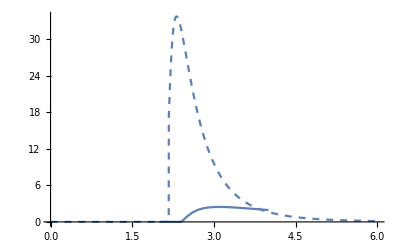

```mathematica
Show[{Plot[sigma[eCM,p[938],Δ[1232],matrixElementpDelta[eCM]],{eCM,0.,6.0},PlotRange->All,PlotStyle->Dashed],pltDeltaDelta}]
```